Partial Differential Equations

Practical File

Name : Ayush Sharma 
Roll No : 2024/12/102

Practical 1 
General Solutions of 1^stand 2^nd order Partial Differential equations

Question 1 
Find general solution of partial differential equation x∂_x u[x,y]+y∂_y u[x,y]=2xy

```mathematica
pde=x*D[u[x,y],x]+y*D[u[x,y],y]==2*x*y;
sol=DSolve[pde,u[x,y],{x,y}];
Print["General solution of given partial differential equation is : ",sol]
```

General solution of given partial differential equation is : {{u[x,y]→x y+C[1][y/x]}}

Question 2
Find general solution of partial differential equation 3∂_x u[x,y]+2∂_y u[x,y]=0

```mathematica
pde=3*D[u[x,y],x]+2*D[u[x,y],y]==0;
sol=DSolve[pde,u[x,y],{x,y}];
Print["General solution of given partial differential equation is : ",sol]
```

General solution of given partial differential equation is : {{u[x,y]→C[1][-(2 x)/3+y]}}

Question 3
Find general solution of partial differential equation u_x+xu_y=0

```mathematica
pde=D[u[x,y],x]+x*D[u[x,y],y]==0;
sol=DSolve[pde,u[x,y],{x,y}];
Print["General solution of given partial differential equation is : ",sol]
```

General solution of given partial differential equation is : {{u[x,y]→C[1][-x^2/2+y]}}

Question 4
Find general solution of partial differential equation u_tt=u_xx

```mathematica
pde=D[u[x,t],{t,2}]==D[u[x,t],{x,2}];
sol=DSolve[pde,u[x,t],{x,t}];
Print["General solution of given partial differential equation is : ",sol]
```

General solution of given partial differential equation is : {{u[x,t]→C[1][t-x]+C[2][t+x]}}

Question 5 
Find general solution of partial differential equation u_tt=9 u_xx

```mathematica
pde=D[u[x,t],{t,2}]==9*D[u[x,t],{x,2}];
sol=DSolve[pde,u[x,t],{x,t}];
Print["General solution of given partial differential equation is : ",sol]
```

General solution of given partial differential equation is : {{u[x,t]→C[1][t-x/3]+C[2][t+x/3]}}

Question 6
Find general solution of partial differential equation u_tt=4 u_xx

```mathematica
pde=D[u[x,t],{t,2}]==4*D[u[x,t],{x,2}];
sol=DSolve[pde,u[x,t],{x,t}];
Print["General solution of given partial differential equation is : ",sol]
```

General solution of given partial differential equation is : {{u[x,t]→C[1][t-x/2]+C[2][t+x/2]}}

Practical 2
Solution and plotting of Cauchy problem for first order PDE.

Question 1 
Solve the Cauchy problem u_x+xu_y=y,u(0,y)=y^2 and plot the solution also.

```mathematica
pde=D[u[x,y],x]+x*D[u[x,y],y]==y;
sol=DSolve[{pde,u[0,y]==y^2},u[x,y],{x,y}];
Print["Solution of given cauchy problem is : ",sol]
Plot3D[u[x,y]/.sol,{x,-3,3},{y,-5,5},AxesLabel->{x,y,u}]
```

Solution of given cauchy problem is : {{u[x,y]→1/12 (-4 x^3+3 x^4+12 x y-12 x^2 y+12 y^2)}}

-Graphics3D-

Question 2
Solve the Cauchy problem u_x+u_y=1,u(x,0)=x^2 and plot the solution also.

```mathematica
pde=D[u[x,y],x]+D[u[x,y],y]==1;
sol=DSolve[{pde,u[x,0]==x^2},u[x,y],{x,y}];
Print["Solution of given cauchy problem is : ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

Solution of given cauchy problem is : {{u[x,y]→x^2+y-2 x y+y^2}}

-Graphics3D-

Question 3
Solve the Cauchy problem u_x+xu_y=0,u(0,y)=Sin y and plot the solution also.

```mathematica
pde=D[u[x,y],x]+x*D[u[x,y],y]==0;
sol=DSolve[{pde,u[0,y]==Sin[y]},u[x,y],{x,y}];
Print["Solution of given cauchy problem is : ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

Solution of given cauchy problem is : {{u[x,y]→-Sin[x^2/2-y]}}

-Graphics3D-

Question 4
Solve the Cauchy problem yu_x+xu_y=0,u(0,y)=Exp[-y^2]  and plot the solution also.

```mathematica
pde=y*D[u[x,y],x]+x*D[u[x,y],y]==0;
sol=DSolve[{pde,u[0,y]==Exp[-y^2]},u[x,y],{x,y}];
Print["Solution of given cauchy problem is : ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

Solution of given cauchy problem is : {{u[x,y]→ⅇ^(x^2-y^2)}}

-Graphics3D-

Question 5
Solve the Cauchy problem u_x+2 u_y=0,u(x,0)=Sin x and plot the solution also.

```mathematica
pde=D[u[x,y],x]+2*D[u[x,y],y]==0;
sol=DSolve[{pde,u[x,0]==Sin[x]},u[x,y],{x,y}];
Print["Solution of given cauchy problem is : ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

Solution of given cauchy problem is : {{u[x,y]→Sin[1/2 (2 x-y)]}}

-Graphics3D-

Question 6 
Solve the Cauchy problem (1 + x^2)u_x+xu_y=0,u(0,y)=y and plot the solution also.

```mathematica
pde=(1+x^2)*D[u[x,y],x]+x*D[u[x,y],y]==0;
sol=DSolve[{pde,u[0,y]==y},u[x,y],{x,y}];
Print["Solution of given cauchy problem is : ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

Solution of given cauchy problem is : {{u[x,y]→1/2 (2 y-Log[1+x^2])}}

-Graphics3D-

Question 7
Solve the Cauchy problem u_x+2 xu_y=2xu,u(x,0)=x^2 and plot the solution also.

```mathematica
pde=D[u[x,y],x]+2*x*D[u[x,y],y]==2*x*u[x,y];
sol=DSolve[{pde,u[x,0]==x^2},u[x,y],{x,y}];
Print["Solution of given cauchy problem is : ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

Solution of given cauchy problem is : {{u[x,y]→-ⅇ^y (-x^2+y)}}

-Graphics3D-

Question 8 
Solve the Cauchy problem u_x+3 u_y=u,u(x,y)=Cos x on y=x and plot the solution also.

```mathematica
pde=D[u[x,y],x]+3*D[u[x,y],y]==u[x,y];
sol=DSolve[{pde,u[x,x]==Cos[x]},u[x,y],{x,y}];
Print["Solution of given cauchy problem is : ",sol]
Plot3D[u[x,y]/.sol,{x,-4,4},{y,-6,6},AxesLabel->{x,y,u}]
```

Solution of given cauchy problem is : {{u[x,y]→ⅇ^(-x/2+y/2) Cos[1/2 (3 x-y)]}}

-Graphics3D-

Practical 3 
Plotting the characteristics for the first order partial differential equations

Question 1 
Plot the characteristics for the first order PDE : u_x-u_y=1

```mathematica
pde=D[u[x,y],x]-D[u[x,y],y]==1;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→x+C[1][x+y]}}

```mathematica
f0=ContourPlot3D[u-x,{u,0,1},{x,0,1},
{y,0,1},ImageSize->{250,250},AxesLabel->{"x","y","u"}];
f1=ContourPlot3D[x+y,{u,0,1},{x,0,1},
{y,0,1},ImageSize->{250,250},AxesLabel->{"x","y","u"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

Question 2
Plot the characteristics for the first order PDE : (1+x^2)u_x+u_y=0

```mathematica
pde=(1+x^2)*D[u[x,y],x]+D[u[x,y],y]==0;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→C[1][y-ArcTan[x]]}}

```mathematica
f0=ContourPlot3D[u,{u,0,1},{x,0,1},
{y,0,1},ImageSize->{250,250},AxesLabel->{"x","y","u"}];
f1=ContourPlot3D[y-ArcTan[x],{u,0,1},{x,0,1},
{y,0,1},ImageSize->{250,250},AxesLabel->{"x","y","u"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

Question 3 
Plot the characteristics for the first order PDE : xu_x+yu_y=2xy

```mathematica
pde=x*D[u[x,y],x]+y*D[u[x,y],y]==2*x*y;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→x y+C[1][y/x]}}

```mathematica
f0=ContourPlot3D[u-x*y,{u,0,2},{x,0,1},
{y,0,2},ImageSize->250,AxesLabel->{"x","y","u"}];
f1=ContourPlot3D[y/x,{u,-1,2},{x,0.1,0.5},
{y,-1,2},ImageSize->250,AxesLabel->{"x","y","u"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

Question 4 
Plot the characteristics for the first order PDE : xu_x+(x+y)u_y=u+1

```mathematica
pde=x*D[u[x,y],x]+(x+y)*D[u[x,y],y]==u[x,y]+1;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→-1+x C[1][y/x-Log[x]]}}

```mathematica
f0=ContourPlot3D[(u+1)/x,{u,-1,2},{x,0.1,0.5},
{y,0,1},ImageSize->250,AxesLabel->{"x-axis","y-axis","u-axis"}];
f1=ContourPlot3D[(y-x*Log[x])/x,{u,0,1},{x,0.1,0.5},
{y,0,1},ImageSize->250,AxesLabel->{"x-axis","y-axis","u-axis"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

Question 5
Plot the characteristics for the first order PDE : xu_x+yu_y=0

```mathematica
pde=x*D[u[x,y],x]+y*D[u[x,y],y]==0;
sol=DSolve[pde,u[x,y],{x,y}]
```

{{u[x,y]→C[1][y/x]}}

```mathematica
f0=ContourPlot3D[u,{u,0,1},{x,0,1},
{y,0,1},ImageSize->250,AxesLabel->{"x-axis","y-axis","u-axis"}];
f1=ContourPlot3D[y/x,{u,0,1},{x,0.1,0.5},
{y,0,1},ImageSize->250,AxesLabel->{"x-axis","y-axis","u-axis"}];
Print[f0,f1]
```

-Graphics3D--Graphics3D-

Practical 4 
Solution of vibrating string problem using D’Alembert formula with initial conditions.
Find the D’Almbert solution of the wave equation u_tt=c^2 u_xx  subjected to u(x,0)=f(x) , u_t(x,0)=g(x) : x∈ R, t>0

Question 1
u_tt=u_xx, u(x,0)=0, u_t(x,0)=x^2, x∈R ,t>0

```mathematica
DSolve[D[u[x,t],{t,2}]==D[u[x,t],{x,2}],u[x,t],{x,t}]
```

{{u[x,t]→C[1][t-x]+C[2][t+x]}}

```mathematica
da[c_,f_,g_,x_,t_]:=
1/2((f/.x->x+c*t)+(f/.x->x-c*t))+1/(2*c)*Integrate[g,{x,x-c*t,x+c*t}]
da[1,0,x^2,x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel->{t,x,u}]
```

1/2 (-1/3 (-t+x)^3+1/3 (t+x)^3)

-Graphics3D-

Question 2 
u_tt=u_xx, u(x,0)=Sin[x], u_t(x,0)=Cos[x], x∈R ,t>0

```mathematica
DSolve[D[u[x,t],{t,2}]==D[u[x,t],{x,2}],u[x,t],{x,t}]
da[c_,f_,g_,x_,t_]:=
1/2((f/.x->x+c*t)+(f/.x->x-c*t))+1/(2*c)*Integrate[g,{x,x-c*t,x+c*t}]
da[1,Sin[x],Cos[x],x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel->{t,x,u}]
```

{{u[x,t]→C[1][t-x]+C[2][t+x]}}

Cos[x] Sin[t]+1/2 (-Sin[t-x]+Sin[t+x])

-Graphics3D-

Question 3 
u_tt=u_xx, u(x,0)=Sin[x], u_t(x,0)=x, x∈R ,t>0

```mathematica
DSolve[D[u[x,t],{t,2}]==D[u[x,t],{x,2}],u[x,t],{x,t}]
da[c_,f_,g_,x_,t_]:=
1/2((f/.x->x+c*t)+(f/.x->x-c*t))+(1/(2*c))*Integrate[g,{x,x-c*t,x+c*t}]
da[1,Sin[x],x,x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel->{t,x,u}]
```

{{u[x,t]→C[1][t-x]+C[2][t+x]}}

1/2 (-1/2 (-t+x)^2+1/2 (t+x)^2)+1/2 (-Sin[t-x]+Sin[t+x])

-Graphics3D-

Question 4 
u_tt=9 u_xx, u(x,0)=Cos[x], u_t(x,0)=Sin[2x], x∈R ,t>0

```mathematica
DSolve[D[u[x,t],{t,2}]==9*D[u[x,t],{x,2}],u[x,t],{x,t}]
da[c_,f_,g_,x_,t_]:=
1/2((f/.x->x+c*t)+(f/.x->x-c*t))+(1/(2*c))*Integrate[g,{x,x-c*t,x+c*t}]
da[3,Cos[x],Sin[2x],x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel->{t,x,u}]
```

{{u[x,t]→C[1][t-x/3]+C[2][t+x/3]}}

1/2 (Cos[3 t-x]+Cos[3 t+x])+1/6 Sin[6 t] Sin[2 x]

-Graphics3D-

Question 5 
u_tt=4 u_xx, u(x,0)=Cosh[x], u_t(x,0)=2x, x∈R ,t>0

```mathematica
DSolve[D[u[x,t],{t,2}]==4*D[u[x,t],{x,2}],u[x,t],{x,t}]
da[c_,f_,g_,x_,t_]:=
1/2((f/.x->x+c*t)+(f/.x->x-c*t))+1/(2*c)*Integrate[g,{x,x-c*t,x+c*t}]
da[2,Cosh[x],2x,x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel->{t,x,u}]
```

{{u[x,t]→C[1][t-x/2]+C[2][t+x/2]}}

1/2 (-1/2 (-2 t+x)^2+1/2 (2 t+x)^2)+1/2 (Cosh[2 t-x]+Cosh[2 t+x])

-Graphics3D-

Question 6 
u_tt=49 u_xx, u(x,0)=Cos[3x], u_t(x,0)=x, x∈R ,t>0

```mathematica
DSolve[D[u[x,t],{t,2}]==49*D[u[x,t],{x,2}],u[x,t],{x,t}]
da[c_,f_,g_,x_,t_]:=
1/2((f/.x->x+c*t)+(f/.x->x-c*t))+(1/(2*c))*Integrate[g,{x,x-c*t,x+c*t}]
da[7,Cos[3x],x,x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel->{t,x,u}]
```

{{u[x,t]→C[1][t-x/7]+C[2][t+x/7]}}

1/14 (-1/2 (-7 t+x)^2+1/2 (7 t+x)^2)+1/2 (Cos[3 (-7 t+x)]+Cos[3 (7 t+x)])

-Graphics3D-

Question 7 
u_tt=16 u_xx, u(x,0)=Cos[x], u_t(x,0)=x.Exp[x], x∈R ,t>0

```mathematica
DSolve[D[u[x,t],{t,2}]==16*D[u[x,t],{x,2}],u[x,t],{x,t}]
da[c_,f_,g_,x_,t_]:=
1/2((f/.x->x+c*t)+(f/.x->x-c*t))+(1/(2*c))*Integrate[g,{x,x-c*t,x+c*t}]
da[4,Cos[x],x*Exp[x],x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel->{t,x,u}]
```

{{u[x,t]→C[1][t-x/4]+C[2][t+x/4]}}

1/2 (Cos[4 t-x]+Cos[4 t+x])+1/4 ⅇ^x (4 t Cosh[4 t]+(-1+x) Sinh[4 t])

-Graphics3D-

Question 8
u_tt=9 u_xx, u(x,0)=x^3, u_t(x,0)=xCos[x], x∈R ,t>0

```mathematica
DSolve[D[u[x,t],{t,2}]==9*D[u[x,t],{x,2}],u[x,t],{x,t}]
da[c_,f_,g_,x_,t_]:=
1/2((f/.x->x+c*t)+(f/.x->x-c*t))+(1/(2*c))*Integrate[g,{x,x-c*t,x+c*t}]
da[3,x^3,x*Cos[x],x,t]
Plot3D[%,{t,1,8},{x,-8,8},AxesLabel->{t,x,u}]
```

{{u[x,t]→C[1][t-x/3]+C[2][t+x/3]}}

1/2 ((-3 t+x)^3+(3 t+x)^3)+1/6 (2 Sin[3 t] (x Cos[x]-Sin[x])+6 t Cos[3 t] Sin[x])

-Graphics3D-

Practical 5 
Solution of heat equation u_t=ku_xx  with initial conditions

Question 1
u_t=1/2 u_xx, u(x,0)=Sin^2 x, u(0,t)=0, u(Pi,t)=0, 0<x<Pi, t>0

```mathematica
eqn={D[u[x,t],t]==(1/2)*D[u[x,t],{x,2}],
u[x,0]==(Sin[x])^2,u[0,t]==0,u[Pi,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,Pi},{t,0,4}];
Plot3D[u[x,t]/.sol,{x,0,Pi},{t,0,4},AxesLabel->{x,t,u}]
```

-Graphics3D-

Question 2
u_t=4 u_xx, u(x,0)=x^2-x^3, u(0,t)=0, u(1,t)=0, 0<x<1, t>0

```mathematica
eqn={D[u[x,t],t]==4*D[u[x,t],{x,2}],
u[x,0]==x^2-x^3,u[0,t]==0,u[1,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,5}];
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,5},AxesLabel->{x,t,u}]
```

-Graphics3D-

Practical 6 
Solution of one-dimensional wave equation u_tt=c^2 u_xx with initial conditions:
(i) u(x,0)=f(x),u_t(x,0)=g(x): x∈R,t>0
(ii) u(x,0)=f(x),u_t(x,0)=g(x),u(0,t)=0: x∈R,t>0
(iii)u(x,0)=f(x),u_t(x,0)=g(x),u_x(0,t)=0: x∈R,t>0

Question 1 
u_tt-u_xx=0, u(x,0)=3Sin[x],u_t(x,0)=x^4; 0<x<1,t>0;

```mathematica
eqn={D[u[x,t],{t,2}]==4*D[u[x,t],{x,2}],
u[x,0]==3Sin[x],Derivative[0,1][u][x,0]==x^4};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{t,0,4},{x,0,1},AxesLabel->{"t","x","u"},
Ticks->{{0,1,2,3,4},{0,1},{-3,0}}]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

-Graphics3D-

Question 2 
u_tt-4 u_xx=0, u(x,0)=Log10[x+1],u_t(x,0)=x; 0<x<1,t>0;

```mathematica
eqn={D[u[x,t],{t,2}]==4*D[u[x,t],{x,2}],
u[x,0]==Log10[x+1],Derivative[0,1][u][x,0]==x};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{t,0,4},{x,0,1},AxesLabel->{"t","x","u"},
Ticks->{{0,1,2,3,4},{0,1},{-3,0}}]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

-Graphics3D-

Question 3
u_tt-9 u_xx=0, u(x,0)=x^3(1-x^2),u_t(x,0)=x^2,u(0,t)=0 :  0<x<1,t>0;

```mathematica
eqn={D[u[x,t],{t,2}]==4*D[u[x,t],{x,2}],
u[x,0]==x^3(1-x^2),Derivative[0,1][u][x,0]==x^2,u[0,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{t,0,4},{x,0,1},AxesLabel->{"t","x","u"},
Ticks->{{0,1,2,3,4},{0,1},{-3,0}}]
```

-Graphics3D-

Question 4
u_tt-16 u_xx=0, u(x,0)=x(1-x),u_t(x,0)=0, u(0,t) =0: 0<x<1,t>0;

```mathematica
eqn={D[u[x,t],{t,2}]==16*D[u[x,t],{x,2}],
u[x,0]==x(1-x),Derivative[0,1][u][x,0]==0,u[0,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{t,0,4},{x,0,1},AxesLabel->{"t","x","u"},
Ticks->{{0,1,2,3,4},{0,1},{-3,0}}]
```

-Graphics3D-

Question 5 
u_tt-9 u_xx=0, u(x,0)=0 ,u_t(x,0)=x^3, u_x(0,t) =0: 0<x<1,t>0;

```mathematica
eqn={D[u[x,t],{t,2}]==9*D[u[x,t],{x,2}],
u[x,0]==0,Derivative[0,1][u][x,0]==x^3,Derivative[1,0][u][0,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{t,0,4},{x,0,1},AxesLabel->{"t","x","u"},
Ticks->{{0,1,2,3,4},{0,1},{-3,0}}]
```

-Graphics3D-

Question 6 
u_tt-4 u_xx=0, u(x,0)=0,u_t(x,0)=x, u_x(0,t) =0: 0<x<1,t>0;

```mathematica
eqn={D[u[x,t],{t,2}]==4*D[u[x,t],{x,2}],
u[x,0]==0,Derivative[0,1][u][x,0]==x^8,Derivative[1,0][u][0,t]==0};
sol=NDSolve[eqn,u[x,t],{x,0,1},{t,0,4}];
Plot3D[u[x,t]/.sol,{t,0,4},{x,0,1},AxesLabel->{"t","x","u"},
Ticks->{{0,1,2,3,4},{0,1},{-3,0}}]
```

-Graphics3D-

Practical 7 
Solution of traffic flow problem with given initial conditions, and plotting of the characteristic base curves and the traffic density function .

Question 1 
Find the traffic density ρ(x,t) satisfying ρ_t+xSin(t)ρ_x=0, with  initial condition ρ_0(x)=1+1/(1+x^2) .
Plot the characteristics base curves and the traffic density function.

The  Characteristic base curves for the given initial value problem are given by :

```mathematica
charBaseCurves1=DSolve[{x'[t]==x[t]*Sin[t],x[0]==x0},x[t],t]
```

{{x[t]→ⅇ^(1-Cos[t]) x0}}

{5 ⅇ^(1-Cos[t]),10 ⅇ^(1-Cos[t]),15 ⅇ^(1-Cos[t]),20 ⅇ^(1-Cos[t])}

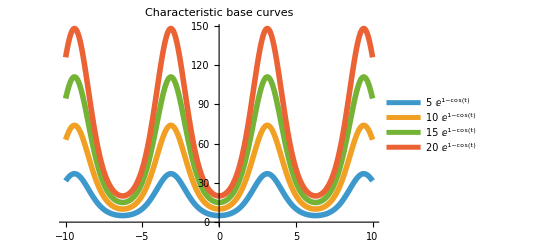

```mathematica
tab=Table[x[t]/.charBaseCurves1[[1]]/.{x0->k},{k,5,20,5}]
Plot[Evaluate[tab],{t,-10,10},PlotStyle->Thickness[0.01],
PlotLegends->Table[tab[[i]],{i,1,4}],
PlotLabel->"Characteristic base curves"]
```

The traffic density function ρ(x,t) or the solution for the given initial value problem are given by:

```mathematica
eqn1=D[ρ[x,t],t]+x*Sin[t]*D[ρ[x,t],x]==0;
sol1=DSolve[{eqn1,ρ[x,0]==1+1/(1+x^2)},ρ[x,t],{x,t}]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{ρ[x,t]→(2 ⅇ^2+ⅇ^(2 Cos[t]) x^2)/(ⅇ^2+ⅇ^(2 Cos[t]) x^2)}}

Hence ρ(x,t) is the traffic density function of the given initial value problem.

```mathematica
Plot3D[ρ[x,t]/.sol1,{x,-10,10},
{t,-10,10},PlotLabel->"Traffic density function"]
```

-Graphics3D-

Question 2 
Find the traffic density ρ(x,t) satisfying ρ_t+e^t ρ_x=2ρ, with  initial condition ρ_0(x)=1+Sin^2(x) .
Plot the characteristics base curves and the traffic density function.

The  Characteristic base curves for the given initial value problem are given by :

```mathematica
charBaseCurves2=DSolve[{x'[t]==Exp[t],x[0]==x0},x[t],t]
```

{{x[t]→-1+ⅇ^t+x0}}

{3+ⅇ^t,7+ⅇ^t,11+ⅇ^t,15+ⅇ^t,19+ⅇ^t}

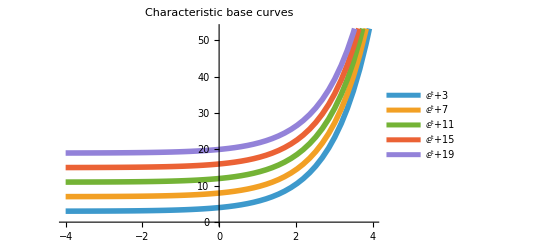

```mathematica
tab=Table[x[t]/.charBaseCurves2[[1]]/.{x0->k},{k,4,20,4}]
Plot[Evaluate[tab],{t,-4,4},PlotStyle->Thickness[0.01],
PlotLegends->Table[tab[[i]],{i,1,5}],
PlotLabel->"Characteristic base curves"]
```

The traffic density function ρ(x,t) or the solution for the given initial value problem are given by:

```mathematica
eqn2=D[ρ[x,t],t]+Exp[t]*D[ρ[x,t],x]==2*ρ[x,t];
sol2=DSolve[{eqn2,ρ[x,0]==1+Sin[x]*Sin[x]},ρ[x,t],{x,t}]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{ρ[x,t]→ⅇ^(2 t) (1+Sin[1-ⅇ^t+x]^2)}}

Hence ρ(x,t) is the traffic density function of the given initial value problem.

```mathematica
Plot3D[ρ[x,t]/.sol2,{x,-4,4},
{t,-1,1},PlotLabel->"Traffic density function"]
```

-Graphics3D-

Question 3 :
Find the traffic density ρ(x,t) satisfying ρ_t+2 ρ_x=0, with  initial condition ρ_0(x)=Exp[-x^2] .
Plot the characteristics base curves and the traffic density function.

The  Characteristic base curves for the given initial value problem are given by :

```mathematica
charBaseCurves3=DSolve[{x'[t]==2,x[0]==x0},x[t],t]
```

{{x[t]→2 t+x0}}

{1+2 t,2+2 t,3+2 t,4+2 t,5+2 t}

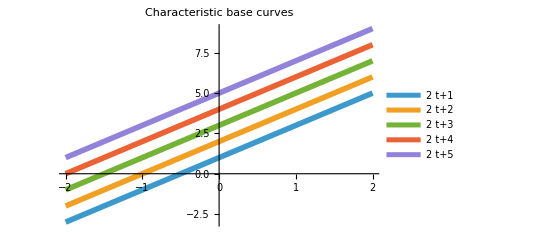

```mathematica
tab=Table[x[t]/.charBaseCurves3[[1]]/.{x0->k},{k,1,5,1}]
Plot[Evaluate[tab],{t,-2,2},PlotStyle->Thickness[0.01],
PlotLegends->Table[tab[[i]],{i,1,5}],
PlotLabel->"Characteristic base curves"]
```

The traffic density function ρ(x,t) or the solution for the given initial value problem are given by:

```mathematica
eqn3=D[ρ[x,t],t]+2*D[ρ[x,t],x]==0;
sol3=DSolve[{eqn3,ρ[x,0]==Exp[-x^2]},ρ[x,t],{x,t}]
```

{{ρ[x,t]→ⅇ^(-4 (t-x/2)^2)}}

Hence ρ(x,t) is the traffic density function of the given initial value problem.

```mathematica
Plot3D[ρ[x,t]/.sol3,{x,-3,3},
{t,-2,2},PlotLabel->"Traffic density function"]
```

-Graphics3D-

Question 4 
Find the traffic density ρ(x,t) satisfying ρ_t+2 t^2*ρ_x=ρ^2, with  initial condition ρ_0(x)=Sin^2(x) .
Plot the characteristics base curves and the traffic density function.

The  Characteristic base curves for the given initial value problem are given by :

```mathematica
charBaseCurves4=DSolve[{x'[t]==2*t^2,x[0]==x0},x[t],t]
```

{{x[t]→1/3 (2 t^3+3 x0)}}

{1/3 (9+2 t^3),1/3 (18+2 t^3),1/3 (27+2 t^3),1/3 (36+2 t^3),1/3 (45+2 t^3)}

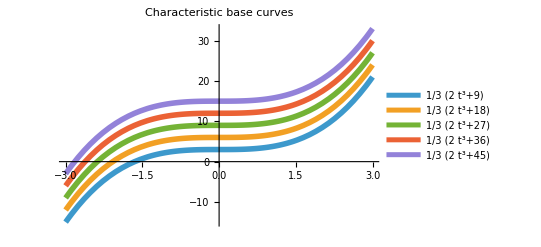

```mathematica
tab=Table[x[t]/.charBaseCurves4[[1]]/.{x0->k},{k,3,15,3}]
Plot[Evaluate[tab],{t,-3,3},PlotStyle->Thickness[0.01],
PlotLegends->Table[tab[[i]],{i,1,5}],
PlotLabel->"Characteristic base curves"]
```

The traffic density function ρ(x,t) or the solution for the given initial value problem are given by:

```mathematica
eqn4=D[ρ[x,t],t]+2*t^2*D[ρ[x,t],x]==ρ[x,t]*ρ[x,t];
sol4=DSolve[{eqn4,ρ[x,0]==Sin[x]*Sin[x]},ρ[x,t],{x,t}]
```

{{ρ[x,t]→1/(-t+Csc[1/3 (-2 t^3+3 x)]^2)}}

Hence ρ(x,t) is the traffic density function of the given initial value problem.

```mathematica
Plot3D[ρ[x,t]/.sol4,{x,-6,6},
{t,-1,1},PlotLabel->"Traffic density function"]
```

-Graphics3D-

Question  5 
Find the traffic density ρ(x,t) satisfying ρ_t+t^2*Cos(t)ρ_x=5, with  initial condition ρ_0(x)=Exp[x] .
Plot the characteristics base curves and the traffic density function.

The  Characteristic base curves for the given initial value problem are given by :

```mathematica
charBaseCurves5=DSolve[{x'[t]==t^2*Cos[t],x[0]==x0},x[t],t]
```

{{x[t]→x0+2 t Cos[t]-2 Sin[t]+t^2 Sin[t]}}

{5+2 t Cos[t]-2 Sin[t]+t^2 Sin[t],10+2 t Cos[t]-2 Sin[t]+t^2 Sin[t],15+2 t Cos[t]-2 Sin[t]+t^2 Sin[t],20+2 t Cos[t]-2 Sin[t]+t^2 Sin[t]}

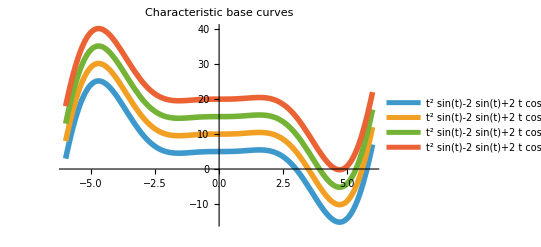

```mathematica
tab=Table[x[t]/.charBaseCurves5[[1]]/.{x0->k},{k,5,20,5}]
Plot[Evaluate[tab],{t,-6,6},PlotStyle->Thickness[0.01],
PlotLegends->Table[tab[[i]],{i,1,4}],
PlotLabel->"Characteristic base curves"]
```

The traffic density function ρ(x,t) or the solution for the given initial value problem are given by:

```mathematica
eqn5=D[ρ[x,t],t]+t^2*Cos[t]*D[ρ[x,t],x]==5;
sol5=DSolve[{eqn5,ρ[x,0]==Exp[x]},ρ[x,t],{x,t}]
```

{{ρ[x,t]→ⅇ^(-2 t Cos[t]-(-2+t^2) Sin[t]) (ⅇ^x+5 ⅇ^(2 t Cos[t]+(-2+t^2) Sin[t]) t)}}

Hence ρ(x,t) is the traffic density function of the given initial value problem.

```mathematica
Plot3D[ρ[x,t]/.sol5,{x,-5,5},
{t,-3,3},PlotLabel->"Traffic density function"]
```

-Graphics3D-